## Notebook Setup

## Pre-amble

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

Inversions::shdw: Symbol Inversions appears in multiple contexts {Combinatorica`,Global`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

## An Introduction to Q-Analysis - Warren P. Johnson

## Chapter 1. Inversions

### 1.1 Stern’s Problem

#### Definition: Inversion

Inversion is a concept in discrete mathematics to measure how much a sequence is out of its natural order.
Definition Inversion: Let p=p1p2···pn be a permutation. We say that (p_i, p_j) is an inversion of p if i < j but p_i > p_j. 
Example: In the permutation {1,3,2}  (p_2,p_3) is an inversion of {1,3,2} since 2 < 3 but p_2 > p_3. ( 3 > 2 ).
The element-based inversion set is essentially the place-based inversion set of the inverse permutation, just with the elements of the pairs exchanged.

#### Formula: Total number of inversions of permutations of length n

I_n= n I_(n-1)+ (n-1!) (n
2)

#### Theorem: Rothe’s Theorem on Conjugate permutations

Conjugate permutations have the same number of inversions

Example:

```mathematica
p={4,5,1,3,2,6};
Inversions[p]
Inversions[InversePermutation[p]]
```

7

7

#### Exc. 1 : Gauss’s Trick

#### Exc. 2 : Prove 1) by Induction

#### Exc. 3 : Prove that (1.1.6) is equivalent to (1.1.4)

#### Exc. 4 : Prove (1.1.6) by the same argument that was used to prove (1.1.4)

#### Exc. 5: Prove that (1.1.6) may be reduced to (1.1.5) if k = n-1

#### Exc. 6: Explain Terquem’s argument

#### Exc. 7: If A_n= I_n/(n!) show that A_n-A_(n-1)= (n-1)/2.

#### Exc. 8: What is the average number of inversions that a permutation of {1, 2, . . . , n} has?

#### Exc. 9: Explain Emeric Deutsch version of (1.1.5)

#### Exc. 10: Derive (1.1.5) from (1.1.1)

#### Exc. 11: Draw the Roethe Diagram of permutation 596381472.

#### Exc. 12: Calculate the number of self-conjugate permutations of {1,2,3, ..., n} for n=1,2,3,4.

#### Exc. 13: Calculate the number of self-conjugate permutations of {1,2,3, ..., n} for n=5.

#### Exc. 14: Calculate the number of self-conjugate permutations of {1,2,3, ..., n} for n in general.

### 1.2 The q-Factorial

#### Definition: the q-Analogue of the number n

#### Definition: the q-Analogue of n!

#### Theorem: Rodrigues’s theorem.

#### Proof of Rodrigues’s theorem.

#### Exc. 1 : Check Rodrigues’Theorem for the cases n=0, 1 and 2.

#### Exc. 2 : Explain why the largest number of inversions that a permutation of {1, 2, . . . , n} can have is (n 2).

#### Exc. 3 : [ TBD ]

#### Exc. 4 : [ TBD ]

#### Exc. 5 : [ TBD ]

#### Exc. 6 : [ TBD ]

#### Exc. 7 : [ TBD ]

#### Exc. 8 : [ TBD ]

#### Exc. 9 : [ TBD ]

#### Exc. 10 : [ TBD ]

#### Exc. 11 : [ TBD ]

#### Exc. 12 : [ TBD ]

#### Exc. 13 : [ TBD ]

#### Exc. 14 : [ TBD ]

#### Exc. 15 : [ TBD ]

#### Exc. 16 : [ TBD ]

#### Exc. 17 : [ TBD ]

#### Exc. 18 : [ TBD ]

#### temp

```mathematica
Factor[1+2 q + 2 q^2 +q^3]
```

(1+q) (1+q+q^2)

```mathematica
Factor[1+q + 2 q^2 +q^3+q^4]
```

(1+q^2) (1+q+q^2)

```mathematica
Factor[1+q + 2 q^2 +2 q^3+2 q^4+q^5+q^6]
```

(1+q^2) (1+q+q^2+q^3+q^4)

```mathematica
Table[Normal[Series[QFactorial[k,q],{q,0,50}]],{k,1,6}]//TableForm
```

1
1+q
1+2 q+2 q^2+q^3
1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6
1+4 q+9 q^2+15 q^3+20 q^4+22 q^5+20 q^6+15 q^7+9 q^8+4 q^9+q^10
1+5 q+14 q^2+29 q^3+49 q^4+71 q^5+90 q^6+101 q^7+101 q^8+90 q^9+71 q^10+49 q^11+29 q^12+14 q^13+5 q^14+q^15

```mathematica
Map[Factor[#]&,Table[Normal[Series[QFactorial[k,q],{q,0,50}]],{k,1,6}]]//TableForm
```

1
1+q
(1+q) (1+q+q^2)
(1+q)^2 (1+q^2) (1+q+q^2)
(1+q)^2 (1+q^2) (1+q+q^2) (1+q+q^2+q^3+q^4)
(1+q)^3 (1+q^2) (1-q+q^2) (1+q+q^2)^2 (1+q+q^2+q^3+q^4)

## TEMP

```mathematica
g=PermutationGraph[p]
```

⁃Graph:<7,6,Undirected>⁃

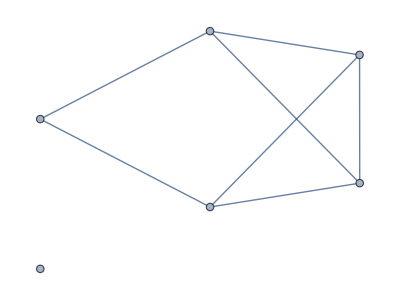

```mathematica
p={4,5,1,3,2,6};
ResourceFunction["PermutationGraph"][p]
```